```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ListAnimate[ListLinePlot[FractionalPart[GoldenRatio*#1]&/@Range[#1],PlotRange->{{0,32},{0,1}},ImageSize->{500,400}]&/@Range[32]]
```

```mathematica
Export["golden_sequence_lines.gif",ListLinePlot[FractionalPart[GoldenRatio*#1]&/@Range[#1],PlotRange->{{0,32},{0,1}},ImageSize->{500,400}]&/@Range[32],"DisplayDurations"->0.7];
```

```mathematica
ListAnimate[{ListPlot[N[FractionalPart[GoldenRatio*#1]&/@Range[#1]],Filling->Axis,PlotRange->{{0,32},{0,1}},ImageSize->{500,400}],ListPlot[Sort[N[FractionalPart[GoldenRatio*#1]&/@Range[#1]]],Filling->Axis,PlotRange->{{0,32},{0,1}},ImageSize->{500,400}]}&/@Range[32]]
Export["golden_sequence_comparison.gif",{ListPlot[N[FractionalPart[GoldenRatio*#1]&/@Range[#1]],Filling->Axis,PlotRange->{{0,32},{0,1}},ImageSize->{500,400}],ListPlot[Sort[N[FractionalPart[GoldenRatio*#1]&/@Range[#1]]],Filling->Axis,PlotRange->{{0,32},{0,1}},ImageSize->{500,400}]}&/@Range[32],"DisplayDurations"->0.7];
```

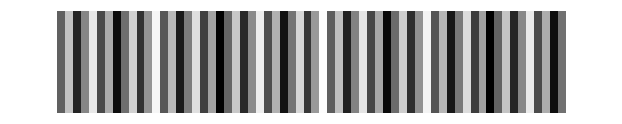

```mathematica
ArrayPlot[{FractionalPart[GoldenRatio*#1]&/@Range[64]}]
```

```mathematica
MyPeriodogram[x_,col_:Black,range_:All]:=ListPlot[Abs@Fourier[x][[;;Ceiling[Dimensions[x][[1]]/2]]],PlotRange->range,Filling->Axis,FillingStyle->{Thickness[0.05],col}]
```

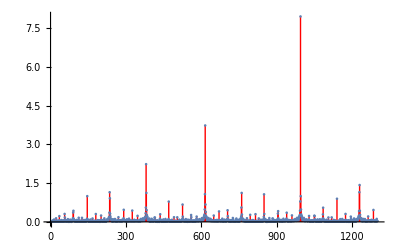

```mathematica
MyPeriodogram[FractionalPart[GoldenRatio*#1]&/@Range[2600]-0.5,Red]
```

```mathematica
N[Abs[FractionalPart[GoldenRatio*(#1+1)]-FractionalPart[GoldenRatio*#1]]]&/@Range[8]
```

{0.381966,0.618034,0.381966,0.381966,0.618034,0.381966,0.618034,0.381966}